# Flatland Semi-infinite medium, Normally-incidence search light illumination, Isotropic Scattering

## Exponential Random Flight

This is code to accompany the book:
A Hitchhiker’s Guide to Multiple Scattering
© 2015 Eugene d’Eon 
www.eugenedeon.com

## Path Setup

Put a file at ~/.hitchhikerpath with the path to your hitchhiker repo so that these worksheets can find the MC data from the C++ simulations for verification

```mathematica
SetDirectory[Import["~/.hitchhikerpath"]]
```

/Users/eug/Documents/research/hitchhikersscatter

## Notation

TODO: new figure

α - single-scattering albedo
Σt - extinction coefficient
r - radial surface coordinate (distance from source of illumination)
θ - direction parameter - angle measured from surface normal

## Analytic

### Grosjean-style diffusion approximation

```mathematica
infflatlandisopointisoscatter`ϕGrosjean[r_,Σt_,α_]:=Exp[-r Σt]/(2 Pi r)+(α Σt)/((2-α)Pi) BesselK[0,r Σt (√2(√(1-α))/(√(2-α)))]
```

## load MC data

```mathematica
halfspaceflatlandnormalsearchlightisoscatter`ppoints[xs_,dr_,maxx_,Σt_]:=Table[{dr(i)-0.5dr,xs[[i]]/Σt},{i,1,Length[xs]}][[1;;-2]]
```

```mathematica
halfspaceflatlandnormalsearchlightisoscatter`fs=FileNames["code/flatland/halfSpace/NormalSearchlight/data/halfSpaceFlatland_normalSearchlight_isotropicscatter_exponential*"];
```

```mathematica
halfspaceflatlandnormalsearchlightisoscatter`index[x_]:=Module[{data,α,Σt},
data=Import[x,"Table"];
Σt=data[[1,12]];
α=data[[2,3]];
{α,Σt,data}];
halfspaceflatlandnormalsearchlightisoscatter`simulations=halfspaceflatlandnormalsearchlightisoscatter`index/@halfspaceflatlandnormalsearchlightisoscatter`fs;
halfspaceflatlandnormalsearchlightisoscatter`alphas=Union[#[[1]]&/@halfspaceflatlandnormalsearchlightisoscatter`simulations]
```

{0.01,0.1,0.3,0.5,0.7,0.8,0.9,0.95,0.99,0.999}

```mathematica
halfspaceflatlandnormalsearchlightisoscatter`muts=Union[#[[2]]&/@halfspaceflatlandnormalsearchlightisoscatter`simulations]
```

{1,3}

```mathematica
halfspaceflatlandnormalsearchlightisoscatter`maxr=halfspaceflatlandnormalsearchlightisoscatter`simulations[[1]][[3]][[2,5]];halfspaceflatlandnormalsearchlightisoscatter`dr=halfspaceflatlandnormalsearchlightisoscatter`simulations[[1]][[3]][[2,7]];
halfspaceflatlandnormalsearchlightisoscatter`numr=Floor[halfspaceflatlandnormalsearchlightisoscatter`maxr/halfspaceflatlandnormalsearchlightisoscatter`dr];
```

## Testbed

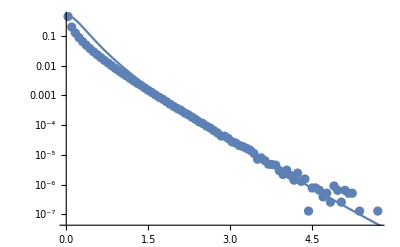

```mathematica
i=10;
sim=halfspaceflatlandnormalsearchlightisoscatter`simulations[[i]];
c=sim[[1]];
Σt=sim[[2]];
data=sim[[3]];
maxr=data[[2,5]];
dr=data[[2,7]];
exitantfluxpoints=data[[7]];

Show[
ListLogPlot[halfspaceflatlandnormalsearchlightisoscatter`ppoints[exitantfluxpoints,dr,maxr,mut],PlotRange->All],
LogPlot[((ⅇ^(-√(r^2+1/Σt^2) Σt))/(2 π (r^2+1/Σt^2))+(ⅇ^(-√(r^2+1/Σt^2) Σt))/(2 π (r^2+1/Σt^2)^(3/2) Σt)+(√2 √(1-c) c Σt BesselK[1,(√2 √(1-c) √(r^2+1/Σt^2) Σt)/(√(2-c))])/((2-c)^(3/2) π √(r^2+1/Σt^2)))c/Pi,{r,0,maxr},PlotRange->All]
]
```